```mathematica
nPoly = 2; (*Highest Hermite polynomial to be used for ReLU approximation*)


(*ReLU and its approximation with Hermite polynomials*)
ReLU[x_]:= Max[0,x];
```

```mathematica
c[n_]:= Integrate[ t*HermiteH[n,t]*Exp[-t^2], {t,0,+Infinity}]/Sqrt[Sqrt[π]*2^n*Factorial[n]];
```

1/(4 √π)+y/2+y^2/(2 √π)

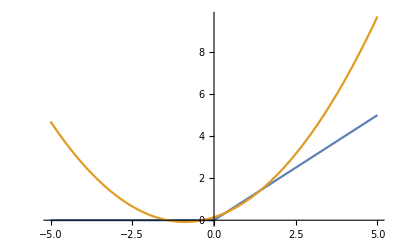

```mathematica
ApproxReLU[n_,x_]:=Expand[Sum[c[i]*HermiteH[i,x]/Sqrt[Sqrt[π]2^i*Factorial[i]],{i,0,n}]];
σ[y_] = ApproxReLU[nPoly,y] (*Activation*)
Plot[{ReLU[x],σ[x]}, {x,-5.,5.}]
```

1/2+y/(√π)

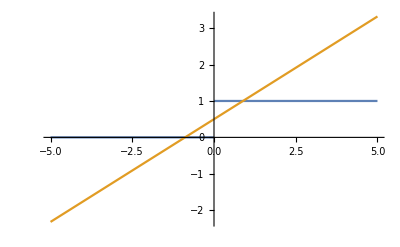

```mathematica
Derσ[y_]=D[σ[y],y]
Plot[{HeavisideTheta[x],Derσ[x]}, {x,-5.,5.}]
```

```mathematica
(*
	This a re actual calculation of all term needed.
	Convetions:
	  - lf[1] and lf[2] will be the local fields of the target, with activation		
*)
<<"/Users/lucaarnaboldi/Desktop/staircase-ss/mathematica/Isserlis.m"
```

```mathematica
target=lf[1] + lf[1]*lf[2];
```

```mathematica
FortranForm[IsserlisTheorem[Derσ[lf[3]]*lf[1]*target]]
```

ω(1,1)/2. + (2*ω(1,2)*ω(1,3))/Sqrt(Pi) + (ω(1,1)*ω(2,3))/Sqrt(Pi)

```mathematica
FortranForm[IsserlisTheorem[Derσ[lf[3]]*lf[2]*target]]
```

ω(1,2)/2. + (ω(1,3)*ω(2,2))/Sqrt(Pi) + (2*ω(1,2)*ω(2,3))/Sqrt(Pi)

```mathematica
IsserlisTheorem[Derσ[lf[3]]*lf[4]*target]
```

1/2 ω[1,4]+(ω[1,4] ω[2,3])/(√π)+(ω[1,3] ω[2,4])/(√π)+(ω[1,2] ω[3,4])/(√π)

```mathematica
FortranForm[IsserlisTheorem[Derσ[lf[3]]*lf[4]*σ[lf[5]]]]
```

ω(3,4)/(4.*Pi) + ω(4,5)/4. + (ω(3,5)*ω(4,5))/Pi + (ω(3,4)*ω(5,5))/(2.*Pi)

```mathematica
FortranForm[IsserlisTheorem[Derσ[lf[3]]*Derσ[lf[4]]*σ[lf[5]]*σ[lf[6]]]]
```

1/(64.*Pi) + ω(3,4)/(16.*Pi**2) + ω(3,5)/(16.*Pi) + ω(3,6)/(16.*Pi) + ω(4,5)/(16.*Pi) + (ω(3,5)*ω(4,5))/(4.*Pi**2) + (ω(3,6)*ω(4,5))/(4.*Pi) + ω(4,6)/(16.*Pi) + 
     -  (ω(3,5)*ω(4,6))/(4.*Pi) + (ω(3,6)*ω(4,6))/(4.*Pi**2) + ω(5,5)/(32.*Pi) + (ω(3,4)*ω(5,5))/(8.*Pi**2) + (ω(3,6)*ω(5,5))/(8.*Pi) + (ω(4,6)*ω(5,5))/(8.*Pi) + 
     -  (ω(3,6)*ω(4,6)*ω(5,5))/(2.*Pi**2) + ω(5,6)/16. + (ω(3,4)*ω(5,6))/(4.*Pi) + (ω(3,5)*ω(5,6))/(4.*Pi) + (ω(3,6)*ω(5,6))/(4.*Pi) + (ω(4,5)*ω(5,6))/(4.*Pi) + 
     -  (ω(3,6)*ω(4,5)*ω(5,6))/Pi**2 + (ω(4,6)*ω(5,6))/(4.*Pi) + (ω(3,5)*ω(4,6)*ω(5,6))/Pi**2 + ω(5,6)**2/(8.*Pi) + (ω(3,4)*ω(5,6)**2)/(2.*Pi**2) + ω(6,6)/(32.*Pi) + 
     -  (ω(3,4)*ω(6,6))/(8.*Pi**2) + (ω(3,5)*ω(6,6))/(8.*Pi) + (ω(4,5)*ω(6,6))/(8.*Pi) + (ω(3,5)*ω(4,5)*ω(6,6))/(2.*Pi**2) + (ω(5,5)*ω(6,6))/(16.*Pi) + 
     -  (ω(3,4)*ω(5,5)*ω(6,6))/(4.*Pi**2)

```mathematica
FortranForm[IsserlisTheorem[Derσ[lf[3]]*Derσ[lf[4]]*σ[lf[5]]*target]]
```

ω(1,2)/(16.*Sqrt(Pi)) + ω(1,3)/(8.*Pi) + ω(1,4)/(8.*Pi) + ω(1,5)/8. + (ω(1,4)*ω(2,3))/(4.*Pi**1.5) + (ω(1,5)*ω(2,3))/(4.*Sqrt(Pi)) + (ω(1,3)*ω(2,4))/(4.*Pi**1.5) + 
     -  (ω(1,5)*ω(2,4))/(4.*Sqrt(Pi)) + (ω(1,3)*ω(2,5))/(4.*Sqrt(Pi)) + (ω(1,4)*ω(2,5))/(4.*Sqrt(Pi)) + (ω(1,5)*ω(2,5))/(4.*Sqrt(Pi)) + (ω(1,2)*ω(3,4))/(4.*Pi**1.5) + 
     -  (ω(1,5)*ω(3,4))/(2.*Pi) + (ω(1,5)*ω(2,5)*ω(3,4))/Pi**1.5 + (ω(1,2)*ω(3,5))/(4.*Sqrt(Pi)) + (ω(1,4)*ω(3,5))/(2.*Pi) + (ω(1,5)*ω(3,5))/(2.*Pi) + 
     -  (ω(1,5)*ω(2,4)*ω(3,5))/Pi**1.5 + (ω(1,4)*ω(2,5)*ω(3,5))/Pi**1.5 + (ω(1,2)*ω(4,5))/(4.*Sqrt(Pi)) + (ω(1,3)*ω(4,5))/(2.*Pi) + (ω(1,5)*ω(4,5))/(2.*Pi) + 
     -  (ω(1,5)*ω(2,3)*ω(4,5))/Pi**1.5 + (ω(1,3)*ω(2,5)*ω(4,5))/Pi**1.5 + (ω(1,2)*ω(3,5)*ω(4,5))/Pi**1.5 + (ω(1,2)*ω(5,5))/(8.*Sqrt(Pi)) + (ω(1,3)*ω(5,5))/(4.*Pi) + 
     -  (ω(1,4)*ω(5,5))/(4.*Pi) + (ω(1,4)*ω(2,3)*ω(5,5))/(2.*Pi**1.5) + (ω(1,3)*ω(2,4)*ω(5,5))/(2.*Pi**1.5) + (ω(1,2)*ω(3,4)*ω(5,5))/(2.*Pi**1.5)

```mathematica
FortranForm[IsserlisTheorem[Derσ[lf[3]]*Derσ[lf[4]]*target^2]]
```

ω(1,1)/4. + ω(1,2)**2/2. + (2*ω(1,2)*ω(1,3))/Sqrt(Pi) + (2*ω(1,2)*ω(1,4))/Sqrt(Pi) + (2*ω(1,3)*ω(1,4))/Pi + (ω(1,1)*ω(2,2))/4. + (2*ω(1,3)*ω(1,4)*ω(2,2))/Pi + 
     -  (ω(1,1)*ω(2,3))/Sqrt(Pi) + (4*ω(1,2)*ω(1,4)*ω(2,3))/Pi + (ω(1,1)*ω(2,4))/Sqrt(Pi) + (4*ω(1,2)*ω(1,3)*ω(2,4))/Pi + (2*ω(1,1)*ω(2,3)*ω(2,4))/Pi + (ω(1,1)*ω(3,4))/Pi + 
     -  (2*ω(1,2)**2*ω(3,4))/Pi + (ω(1,1)*ω(2,2)*ω(3,4))/Pi

```mathematica
FortranForm[IsserlisTheorem[Derσ[lf[3]]*Derσ[lf[4]]]]
```

0.25 + ω(3,4)/Pi

```mathematica
FortranForm[IsserlisTheorem[σ[lf[3]]*σ[lf[4]]]]
```

1/(16.*Pi) + ω(3,3)/(8.*Pi) + ω(3,4)/4. + ω(3,4)**2/(2.*Pi) + ω(4,4)/(8.*Pi) + (ω(3,3)*ω(4,4))/(4.*Pi)

```mathematica
FortranForm[IsserlisTheorem[σ[lf[3]]*target]]
```

ω(1,2)/(4.*Sqrt(Pi)) + ω(1,3)/2. + (ω(1,3)*ω(2,3))/Sqrt(Pi) + (ω(1,2)*ω(3,3))/(2.*Sqrt(Pi))

```mathematica
FortranForm[IsserlisTheorem[target^2]]
```

ω(1,1) + 2*ω(1,2)**2 + ω(1,1)*ω(2,2)